## Cosmological Perturbation Theory Package

First, load the package

```mathematica
<<COSPER
```

Get::noopen: Cannot open "COSPER".

$Failed

Brief on-line help is available for all functions:

```mathematica
?IMetric
```

IMetric[g], with g an n.n-matrix (two lower indices),
  returns the inverse metric (two upper indices).

```mathematica
Needs["PlotLegends`"]
SetDirectory["E:\\Nutshare\\Store\\Projects\\HZ\\PowerSpectrum\\PowerSpectrum_Notes\\Mathematica\\"]
```

E:\Nutshare\Store\Projects\HZ\PowerSpectrum\PowerSpectrum_Notes\Mathematica

## Basic

### Background

First define the coordinate n-vector:

```mathematica
x={t,x1,x2,x3};
```

and then specify the metric as a square n×n matrix:

```mathematica
(met={{-a[t]*a[t],0,0,0},{0,a[t]*a[t],0,0},{0,0,a[t]*a[t],0},{0,0,0,a[t]*a[t]}})//MatrixForm;
```

"IMetric" is the only 1-argument function:

```mathematica
IMetric[met]//MatrixForm;
```

```mathematica
IMetric[met];
```

All other "functions" take two arguments, the metric matrix and then the coordinate vector:

```mathematica
Christoffel[met,x];
```

```mathematica
Riemann[met,x];
```

```mathematica
Ricci[met,x];
```

```mathematica
SCurvature[met,x]
```

(6 a''[t])/a[t]^3

```mathematica
FullSimplify[SCurvature[met,x]];
```

```mathematica
EinsteinTensor[met,x];
```

```mathematica
SqRicci[met,x];
```

```mathematica
SqRiemann[met,x];
```

```mathematica
(EMTensor={{-ρ[t],0,0,0},{0,p[t],0,0},{0,0,p[t],0},{0,0,0,p[t]}})//MatrixForm;
```

Friedmann Equation

```mathematica
FriedmannClassic=EinsteinTensor[met,x][[1]][[1]]==κ^2 EMTensor[[1]][[1]];
```

## ΛCDM Model

Hubble function

```mathematica
HL[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=HCurrent √(Omegam0 a^-3+Omegar0 a^-4+OmegaL);
HL1[a_,HCurrent_,Omegam0_,Omegar0_,OmegaL_]=D[HL[a,HCurrent,Omegam0,Omegar0,OmegaL],a];
iHL[a_]:= H0  √(Ωm0 a^-1+ Ωx0 a^2)
```

```mathematica
HL[a,H0,Ωm0,Ωr0,Ωx0]
HL[a_]=HL[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a,H0,Ωm0,Ωr0,Ωx0]
HL1[a_]=HL1[a,H0,Ωm0,Ωr0,Ωx0]
HM[a_]=HL[a,H0,Ωm0,0,Ωx0]
HM1[a_]=HL1[a,H0,Ωm0,0,Ωx0]
HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]
```

71. √(0.73+0.0000809/a^4+0.27/a^3)

71. √(0.73+0.0000809/a^4+0.27/a^3)

(35.5 (-0.0003236/a^5-0.81/a^4))/(√(0.73+0.0000809/a^4+0.27/a^3))

(35.5 (-0.0003236/a^5-0.81/a^4))/(√(0.73+0.0000809/a^4+0.27/a^3))

71. √(0.73+0.27/a^3)

-28.755/(√(0.73+0.27/a^3) a^4)

-2.14831×10^9

## f(R) Gravity

f(R) signature

```mathematica
Clear[R]
RR[a_,HCurrent_,Constant_,Omegam0_,Omegar0_,curv_]=3 HCurrent^2/c^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant curv/c^2
D[3 HCurrent^2/lightspeed^2(Omegam0 a^-3+Omegar0 a^-4)+2 Constant curv/lightspeed^2,a];
RR1[a_,HCurrent_,Omegam0_,Omegar0_,curv_]=(3 HCurrent^2 (-(3 Omegam0)/a^4-(4 Omegar0)/a^5))/c^2//Simplify
```

(Constant curv)/45000000000+(HCurrent^2 (Omegam0/a^3+Omegar0/a^4))/30000000000

-(HCurrent^2 (3 a Omegam0+4 Omegar0))/(30000000000 a^5)

n is kinda special. Give the value of it first. Because when doing derivative

```mathematica
(*
Clear[f,fR]
(*fComp[Constant1_,Constant2_,mass_]=ffComp[4,Constant1,Constant2,mass]/.{R->R[a]};*)
f[Constant1_,Constant2_,mass_]=
fR[Constant1_,Constant2_,mass_]=ffR[1,Constant1,Constant2,mass]/.{R->R[a]}
fRR[Constant1_,Constant2_,mass_]=ffRR
*)
```

```mathematica
(*
Clear[f1,fR1,fR2]
f1[Constant1_,Constant2_,mass_]=Simplify[D[f[Constant1,Constant2,mass],a]]
fR1[Constant1_,Constant2_,mass_]=D[fR[Constant1,Constant2,mass],a]//Simplify
fR2[Constant1_,Constant2_,mass_]=D[D[fR[Constant1,Constant2,mass],a],a]
*)
```

Constants and fundamental functions. Units should be determined first.

```mathematica
Clear[Const1,Const2,Ω]
c=3*10^5;
h=0.71;
H0=100 h;
Ωx0 =0.73;
Ωm0 =0.27;
Ωr0 =8.09*10^-5;
fR0=0.02;
d1=6 Ωx0/Ωm0;
d2=-fR0 (12/Ωm0-9)^2
Rs=H0^2 Ωm0;
lp=√(2.47*10^-25);
Const1=-(36(Ωx0/Ωm0)^2)/(12/Ωm0-9)^2 1/fR0;
Const2=-(6 Ωx0/Ωm0)/(12/Ωm0-9)^2 1/fR0;
Ω[a_]=Ωm0 a^-3+Ωr0 a^-4;
Ωm[a_]=Ωm0 a^-3
Ωr[a_]=Ωr0 a^-4
R=3 H0^2 Ωm0 a^-3+2d1 Rs;
R1=RR1[a,H0,Ωm0,Ωr0,Rs];
(*
ρcr= (3 H0^2)/κ^2;
ρm[a_]=ρcr Ωm0 a^-3;
ρr[a_]=ρcr Ωr0 a^-4;
ρ[a_]=ρm[a]+ρr[a];
pm[a_]=0;
pr[a_]=1/3 ρr[a];
p[a_]=pm[a]+pr[a];
*)
Hubb[a_]:=HubbleL[Ωr0,Ωm0,Ωx0,H0,a];
```

-25.1262

0.27/a^3

0.0000809/a^4

First equation: (Omega is the parameter for fraction evolution, so use )

```mathematica
f=-d1 Rs/c^2+d1 Rs/c^2 Rs^2/R^2-d1 Rs/c^2(Rs^2/R^2)^2
fR=-2d1 Rs^3 1/R^3+4d1 Rs^5/R^5
fRR=6d1 Rs^3/R^4 c^2
3 (1+fR)==1/2 (-f+(1-fR) R)+κ^2 (ρm[a]+ρr[a])-3 a fRR H[a]^2 R1[a]
```

-2.45329×10^-7-841919./((44159.2+4083.21/a^3)^4)+0.454474/((44159.2+4083.21/a^3)^2)

(3.03091×10^17)/((44159.2+4083.21/a^3)^5)-(8.18054×10^10)/((44159.2+4083.21/a^3)^3)

(2.20874×10^22)/((44159.2+4083.21/a^3)^4)

3 (1+(3.03091×10^17)/((44159.2+4083.21/a^3)^5)-(8.18054×10^10)/((44159.2+4083.21/a^3)^3))==1/2 (2.45329×10^-7+841919./((44159.2+4083.21/a^3)^4)-0.454474/((44159.2+4083.21/a^3)^2)+(1-(3.03091×10^17)/((44159.2+4083.21/a^3)^5)+(8.18054×10^10)/((44159.2+4083.21/a^3)^3)) (44159.2+4083.21/a^3))-(6.62623×10^22 a (5041. (0.0000809/a^4+0.27/a^3)+1/6 (-272.587 (-81-(0.00531441 a^16)/((0.0000809+0.27 a+44159.2 a^4)^4)+(0.6561 a^8)/((0.0000809+0.27 a+44159.2 a^4)^2))+(1.56398×10^-6 (44159.2+0.0000809/a^4+0.27/a^3) a^20 (3.70502×10^6-(2.28705×10^8 (0.0000809+0.27 a+44159.2 a^4)^2)/a^8))/((0.0000809+0.27 a+44159.2 a^4)^5))) (-(1.68033×10^-7 (0.0003236+0.81 a))/a^5)[a])/((44159.2+4083.21/a^3)^4 (1+(0.212868 (-0.0003236/a^5-0.81/a^4) a^17)/((0.0000809+0.27 a+44159.2 a^4)^4)+(1.03417×10^-10 a^20 (3.70502×10^6-(2.28705×10^8 (0.0000809+0.27 a+44159.2 a^4)^2)/a^8))/((0.0000809+0.27 a+44159.2 a^4)^5)))+κ^2 (ρm[a]+ρr[a])

## Background Comparison with LCDM model.

```mathematica
H[a_]=(√(-(2 λ ((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3)) (1/3 (2 Rs λ+3 H0^2 Ω[a])-(3 Rs^2-(-2 Rs λ-3 H0^2 Ω[a])^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+27 H0^2 Rs^2 Ω[a]+36 H0^2 Rs^2 λ^2 Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+27 H0^2 Rs^2 Ω[a]+36 H0^2 Rs^2 λ^2 Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))^(1/3)))/(Rs (1+1/Rs^2((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2)^2)-Rs λ (-1+1/(1+1/Rs^2((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2))+6 H0^2 Ωm[a]+6 H0^2 Ωr[a]))/(√6 √(1-(2 λ ((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3)))/(Rs (1+1/Rs^2((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2)^2)+a ((8 λ ((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2)/(Rs^3 (1+1/Rs^2((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2)^3)-(2 λ)/(Rs (1+1/Rs^2((2 Rs λ)/3+H0^2 Ω[a]+(Rs^2 (-3+4 λ^2)+12 H0^2 Rs λ Ω[a]+9 H0^4 Ω[a]^2)/(3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))+1/3 (-9 Rs^3 λ+8 Rs^3 λ^3+9 H0^2 Rs^2 (3+4 λ^2) Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^2 (-Rs^4 (-1+λ^2)+6 H0^2 Rs^3 λ (-5+4 λ^2) Ω[a]+18 H0^4 Rs^2 (1+6 λ^2) Ω[a]^2+162 H0^6 Rs λ Ω[a]^3+81 H0^8 Ω[a]^4)))^(1/3))^2)^2)) (H0^2 Ω'[a]-(2 H0^2 (-2 Rs λ-3 H0^2 Ω[a]) Ω'[a])/(-9 Rs^3 λ+8 Rs^3 λ^3+27 H0^2 Rs^2 Ω[a]+36 H0^2 Rs^2 λ^2 Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))^(1/3)+((3 Rs^2-(-2 Rs λ-3 H0^2 Ω[a])^2) (27 H0^2 Rs^2 Ω'[a]+36 H0^2 Rs^2 λ^2 Ω'[a]+108 H0^4 Rs λ Ω[a] Ω'[a]+81 H0^6 Ω[a]^2 Ω'[a]+(3 √3 (-30 H0^2 Rs^5 λ Ω'[a]+24 H0^2 Rs^5 λ^3 Ω'[a]+36 H0^4 Rs^4 Ω[a] Ω'[a]+216 H0^4 Rs^4 λ^2 Ω[a] Ω'[a]+486 H0^6 Rs^3 λ Ω[a]^2 Ω'[a]+324 H0^8 Rs^2 Ω[a]^3 Ω'[a]))/(2 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))))/(9 (-9 Rs^3 λ+8 Rs^3 λ^3+27 H0^2 Rs^2 Ω[a]+36 H0^2 Rs^2 λ^2 Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))^(4/3))+(27 H0^2 Rs^2 Ω'[a]+36 H0^2 Rs^2 λ^2 Ω'[a]+108 H0^4 Rs λ Ω[a] Ω'[a]+81 H0^6 Ω[a]^2 Ω'[a]+(3 √3 (-30 H0^2 Rs^5 λ Ω'[a]+24 H0^2 Rs^5 λ^3 Ω'[a]+36 H0^4 Rs^4 Ω[a] Ω'[a]+216 H0^4 Rs^4 λ^2 Ω[a] Ω'[a]+486 H0^6 Rs^3 λ Ω[a]^2 Ω'[a]+324 H0^8 Rs^2 Ω[a]^3 Ω'[a]))/(2 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4)))/(9 (-9 Rs^3 λ+8 Rs^3 λ^3+27 H0^2 Rs^2 Ω[a]+36 H0^2 Rs^2 λ^2 Ω[a]+54 H0^4 Rs λ Ω[a]^2+27 H0^6 Ω[a]^3+3 √3 √(Rs^6-Rs^6 λ^2-30 H0^2 Rs^5 λ Ω[a]+24 H0^2 Rs^5 λ^3 Ω[a]+18 H0^4 Rs^4 Ω[a]^2+108 H0^4 Rs^4 λ^2 Ω[a]^2+162 H0^6 Rs^3 λ Ω[a]^3+81 H0^8 Rs^2 Ω[a]^4))^(2/3)))))/.{λ->d1};
```

```mathematica
H1[a_]=D[H[a],a];
```

```mathematica
H[0.0001]
```

7.37512×10^7

```mathematica
Hb[a_]=√((H0^2 Ω+1/6 (-1/81 Rs λ (-81-(a^16 Rs^4)/(H0^8 (2 a^4 Rs λ+a Ωm0+Ωr0)^4)+(9 a^8 Rs^2)/(H0^4 (2 a^4 Rs λ+a Ωm0+Ωr0)^2))+(2 a^20 Rs^3 λ (2 Rs λ+Ωm0/a^3+Ωr0/a^4) (2 Rs^2-(9 H0^4 (2 a^4 Rs λ+a Ωm0+Ωr0)^2)/a^8))/(81 H0^8 (2 a^4 Rs λ+a Ωm0+Ωr0)^5)))/(1+(2 a^17 Rs^3 λ (-(3 Ωm0)/a^4-(4 Ωr0)/a^5))/(3 H0^6 (2 a^4 Rs λ+a Ωm0+Ωr0)^4)+(2 a^20 Rs^3 λ (2 Rs^2-(9 H0^4 (2 a^4 Rs λ+a Ωm0+Ωr0)^2)/a^8))/(243 H0^10 (2 a^4 Rs λ+a Ωm0+Ωr0)^5)))/.{λ-> d1,Ω->Ω[a]}
```

√((5041. (0.0000809/a^4+0.27/a^3)+1/6 (-272.587 (-81-(0.00531441 a^16)/((0.0000809+0.27 a+44159.2 a^4)^4)+(0.6561 a^8)/((0.0000809+0.27 a+44159.2 a^4)^2))+(1.56398×10^-6 (44159.2+0.0000809/a^4+0.27/a^3) a^20 (3.70502×10^6-(2.28705×10^8 (0.0000809+0.27 a+44159.2 a^4)^2)/a^8))/((0.0000809+0.27 a+44159.2 a^4)^5)))/(1+(0.212868 (-0.0003236/a^5-0.81/a^4) a^17)/((0.0000809+0.27 a+44159.2 a^4)^4)+(1.03417×10^-10 a^20 (3.70502×10^6-(2.28705×10^8 (0.0000809+0.27 a+44159.2 a^4)^2)/a^8))/((0.0000809+0.27 a+44159.2 a^4)^5)))

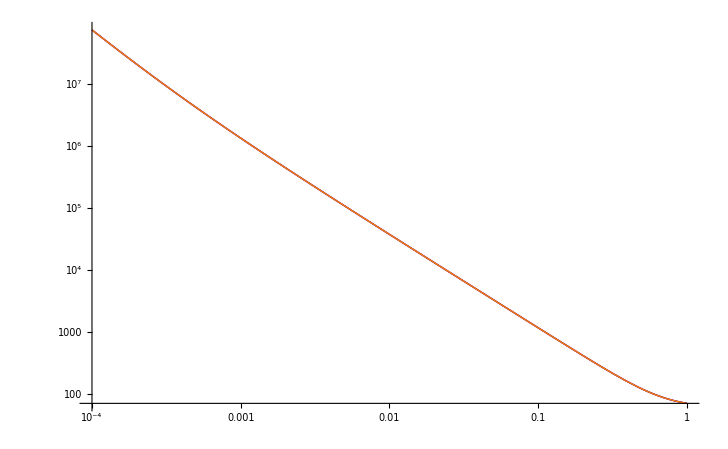

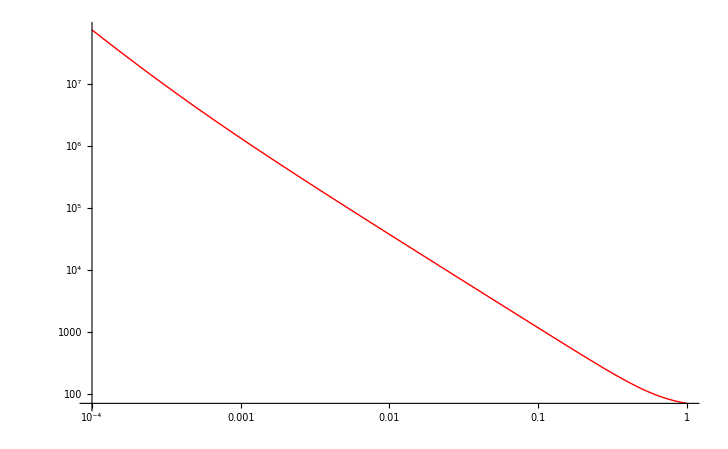

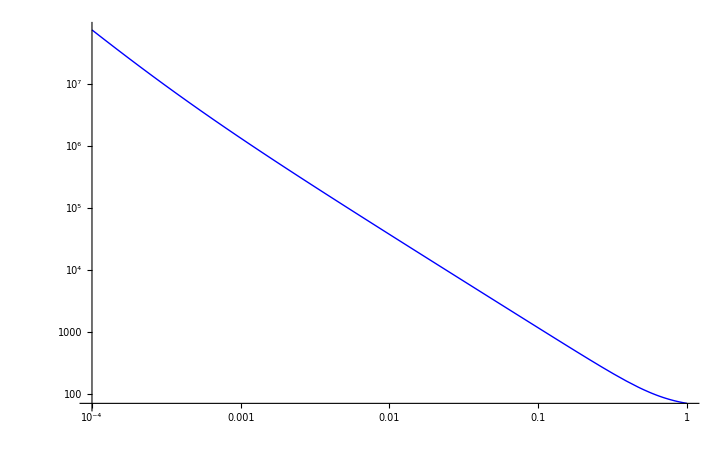

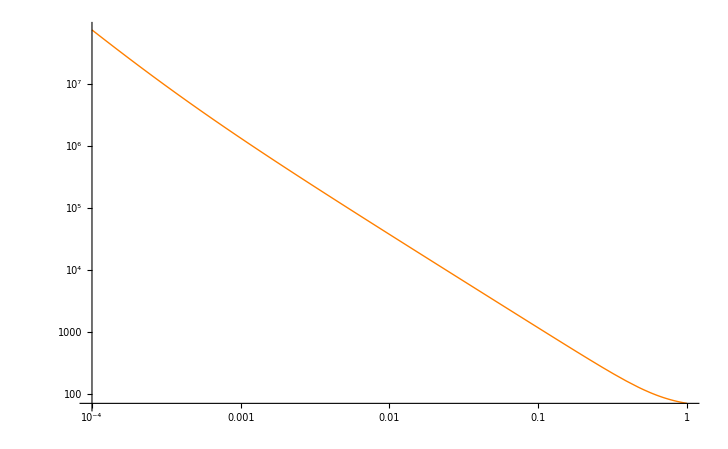

```mathematica
LogLogPlot[{HL[a,H0,Ωm0,Ωr0,Ωx0],H[a],Hb[a]},{a,10^-4,1},PlotStyle->{Red,Blue,Orange}]
LogLogPlot[HL[a,H0,Ωm0,Ωr0,Ωx0],{a,10^-4,1},PlotStyle->Red]
LogLogPlot[H[a],{a,10^-4,1},PlotStyle->Blue]
LogLogPlot[Hb[a],{a,10^-4,1},PlotStyle->Orange]
```

```mathematica
H1[aa]/H[aa]//Simplify
```

$Aborted

H1[a] is the first derivative of H[a]

```mathematica
wleff[a_]=-1-2/3 a HL1[a]/HL[a]
weff[a_]=-1-2/3 a H1[a]/H[a]
```

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

-1-(2 «3» ((-(0.0238375 «1» (-((«1»)«1»«1»)/(9 «1»)+«3»))/((1+«22» («1»)^2)^2)+(«1»)/(«1»)^2-«1»+«1»-(«18»)/(«1»)-24499.3/a^4)/(2 √6 √(«1») √(1-(«21» «1»)/(«1»)^2+(-0.0238375/((1+«22» («1»)^2)^2)+(5.14706×10^-8 «1»)/(1+«1»)^3) («1») a))-(«1»)/(«1»)))/(√(-22079.6 (-1+1/(1+5.39808×10^-7 («1»)^2))-(0.0238375 («1») («1»))/((1+5.39808×10^-7 «1»)^2)+2.4469/a^4+8166.42/a^3))

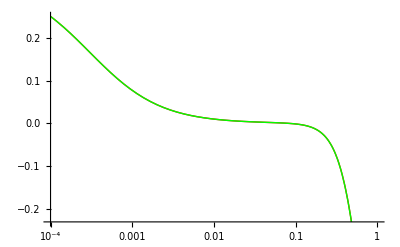

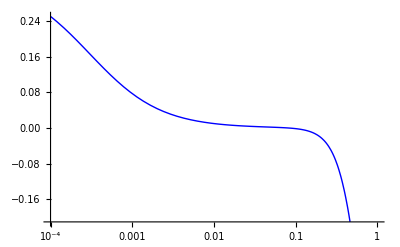

```mathematica
LogLinearPlot[{wleff[a],weff[a]},{a,0.0001,1},PlotStyle->{Red,Green,Blue}]
LogLinearPlot[weff[a],{a,0.0001,1},PlotStyle->{Red,Green,Blue}]
```

```mathematica
weff[0.3]
H1[0.1]
HL1[0.3]
HL[0.3]
H[0.3]
```

-0.0678211

-17519.8

-1084.69

232.681

232.69

## f(R) Gravity Perturbation

LCDM Model data

138

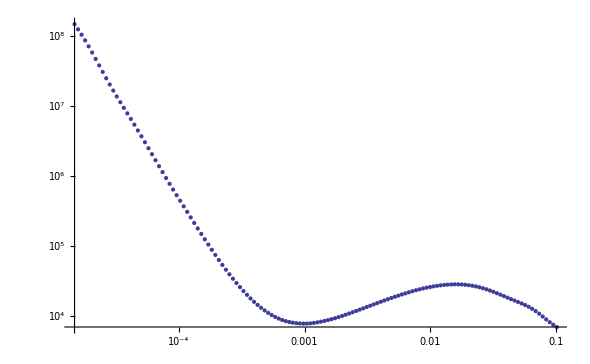

NIntegrate::nlim: temp = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

0.675 √(0.73+0.0000809/a^4+0.27/a^3) NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}]

1. √(0.27/temp+0.73 temp^2)

71. √(0.73+0.0000809/a^4+0.27/a^3)

71. √(0.27/temp+0.73 temp^2)

NIntegrate::nlim: tempo = a is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::nlim: tempo = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

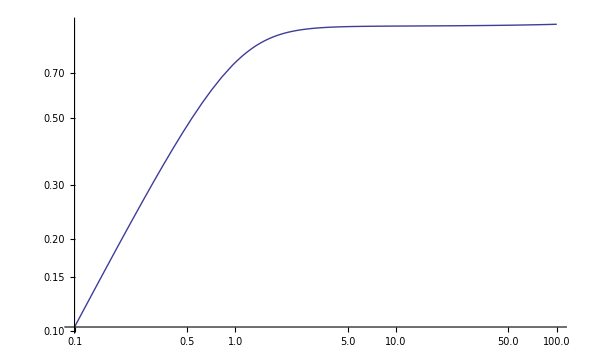

```mathematica
Clear[GrowthL]
PowerL=Import["cdm_invariant_cut.dat"];
lent=Length[PowerL]
ListLogLogPlot[PowerL]
GrowthL[a_]:= 5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[tempo]/H0)^3,{tempo,0,a}]
5/2 Ωm0  HL[a,H0,Ωm0,Ωr0,Ωx0]/H0 NIntegrate[1/(iHL[temp]/H0)^3,{temp,0,a}]
iHL[temp]/H0
HL[a,H0,Ωm0,Ωr0,Ωx0]
iHL[temp]
GrowthL1[a_]=D[GrowthL[a],a];
LogLogPlot[mn GrowthL[1/mn],{mn,0.1,100}]
```

Check the divation from LCDM : M

((8.83498×10^22)/((44159.2+4083.21/a^3)^4)+((1+(3.03091×10^17)/((44159.2+4083.21/a^3)^5)-(2.20874×10^22)/((44159.2+4083.21/a^3)^3)) a^2)/kk^2)/((1+(3.03091×10^17)/((44159.2+4083.21/a^3)^5)-(8.18054×10^10)/((44159.2+4083.21/a^3)^3)) ((6.62623×10^22)/((44159.2+4083.21/a^3)^4)+((1+(3.03091×10^17)/((44159.2+4083.21/a^3)^5)-(2.20874×10^22)/((44159.2+4083.21/a^3)^3)) a^2)/kk^2))

1.00073

1.00073

1.00072

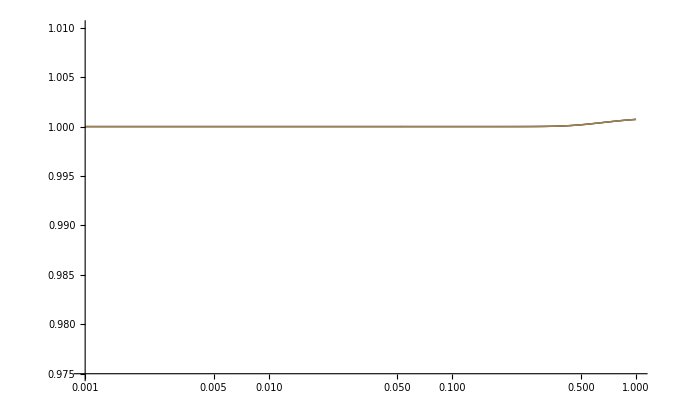

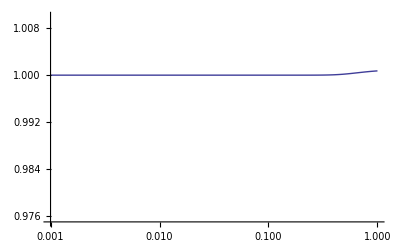
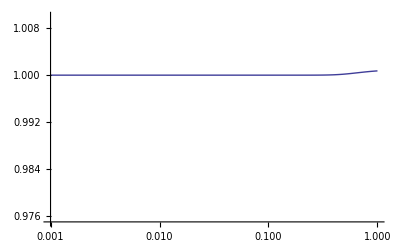
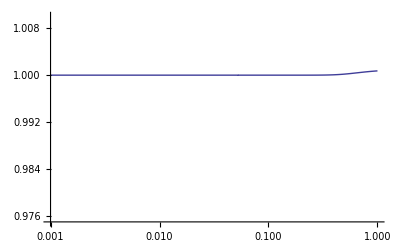

```mathematica
Clear[k,a,dH,dHL,temp,chih2]
dH[a_?NumberQ]:= c a NIntegrate[1/(temp^2 H[temp]),{temp,0,a}]
dHL[a_?NumberQ]:=c a NIntegrate[1/(temp^2 HL[temp]),{temp,0,a}]
k[a_]:=1/dH[a]
kL[a_]:=1/dHL[a]
chih2[a_,kk_]=1/(fR+1)(4fRR+(fR+1-R fRR)a^2/kk^2)/(3fRR+(fR+1-R fRR)a^2/kk^2)//Simplify
chih2[1,0.01]
chih2[1,0.1]
chih2[1,0.5]
LogLinearPlot[{chih2[a,0.001],chih2[a,0.01],chih2[a,0.1]},{a,0.001,1},PlotRange->{0.975,1.01}]
Table[{LogLinearPlot[chih2[a,0.001],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.01],{a,0.001,1},PlotRange->{0.975,1.01}],LogLinearPlot[chih2[a,0.1],{a,0.001,1},PlotRange->{0.975,1.01}]}]
```

```mathematica
(*
xx[a_]=Block[{kk,gg},kk=h PowerL[[100,1]];NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a)gg'[a]-3/2 chih2[a,kk] H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-3]==GrowthL'[10^-3]},gg[a],{a,0.001,10}][[1]][[1]]]
xx[10]
xxx[a_]=Block[{kk=h PowerL[[nn,1]]},NDSolve[{a^2×∂_(a,a) DgL[a]+3/2×a×(1+H[a]^-2×H0^2×Ωx0)×∂_a DgL[a]-3/2×chih2[a,kk]*H[a]^-2×H0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
xxxx[a_]=Block[{kk=h PowerL[[1,1]]},NDSolve[{∂_(a,a) DgL[a]+(3/a+HL1[a]/HL[a])×∂_a DgL[a]-3/2 1/(a^2 HL[a]^2)H0^2×(Ωm0 a^-3+Ωx0)×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL[a],{a,0.001,1}][[1]][[1]]];
*)
```

```mathematica
(*xx[0.1]
GrowthL[0.01]
*)
```

```mathematica
PowerL[[nn,1]]==k[an];
```

Part::pspec: Part specification nn is neither an integer nor a list of integers.

```mathematica
solgf=NDSolve[{a^2*gg''[a]+a^2*(H1[a]/H[a]+3/a)gg'[a]-3/2 H0^2 Ωm0 a^-3/H[a]^2 gg[a]==0,gg[10^-3]==GrowthL[10^-3],gg'[10^-2]==GrowthL'[10^-2]},gg[a],{a,0.001,1}][[1]]
Growth[a_]=gg[a]/.solgf[[1]]
```

NIntegrate::nlim: tempo = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{gg[a]→InterpolatingFunction[{{0.001,1.}},<>][a]}

InterpolatingFunction[{{0.001,1.}},<>][a]

NIntegrate::nlim: tempo = #1 is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

{{DgL→InterpolatingFunction[{{0.001,10.}},<>]}}

NIntegrate::nlim: tempo = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.434321} lies outside the range of data in the interpolating function. Extrapolation will be used.

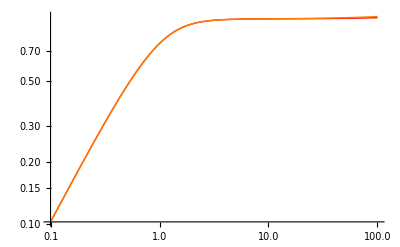

```mathematica
Clear[ggl,solgfl]
(*solgfl=NDSolve[{a^2*ggl''[a]+a^2*((3 H0^2 Ωx0)/(2 a HL[a]^2)+3/(2a))ggl'[a]-3/2 H0^2 Ωm0 a^-3/HL[a]^2 ggl[a]==0,ggl[10^-3]==GrowthL[10^-3],ggl'[10^-3]==GrowthL'[10^-3]},ggl[a],{a,0.001,1}][[1]]
GrowthLt[a_]=ggl[a]/.solgfl[[1]]
*)
solgfl=NDSolve[{a^2×D[DgL[a], a,a]+3/2×a×(1+HL[a]^-2×H0^2×Ωx0)×D[DgL[a], a]-3/2×HL[a]^-2×H0^2×Ωm0 a^-3×DgL[a]==0,DgL[10^-3]==N[GrowthL[10^-3]],DgL'[10^-2]==N[GrowthL'[10^-2]]},DgL,{a,0.001,10}]
GrowthLt[a_]:=DgL[a]/.solgfl[[1]]
LogLogPlot[{mn GrowthL[1/mn],mn GrowthLt[1/mn]},{mn,0.1,100},PlotStyle->{Red,Orange},PlotLegend->{"LCDM_L", "L"},LegendPosition->{1.1,-0.4}]
```

NIntegrate::nlim: tempo = 1/mn is not a valid limit of integration.

General::stop: Further output of NIntegrate :: nlim will be suppressed during this calculation.

InterpolatingFunction::dmval: Input value {-0.217156} lies outside the range of data in the interpolating function. Extrapolation will be used.

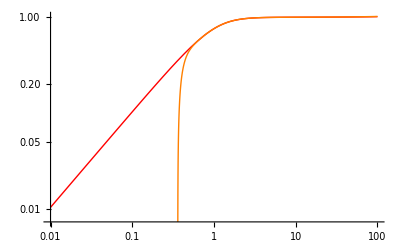

InterpolatingFunction::dmval: Input value {-0.217156} lies outside the range of data in the interpolating function. Extrapolation will be used.

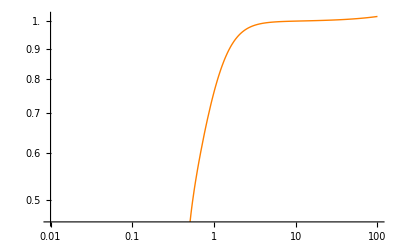

```mathematica
LogLogPlot[{mn GrowthL[1/mn],mn Growth[1/mn]},{mn,0.01,100},PlotStyle->{Red,Orange},PlotLegend->{"LCDM_L", "f(R)"},
LegendPosition->{1.1,-0.4}]
LogLogPlot[mn Growth[1/mn],{mn,0.01,100},PlotStyle->{Red,Orange},PlotLegend-> "f(R)",LegendPosition->{1.1,-0.4}]
```

```mathematica
ain=Table[ai/.FindRoot[PowerL[[i,1]]h==k[ai],{ai,0.0001}],{i,1,lent}]
aL=Table[aL/.FindRoot[PowerL[[i,1]]h==kL[aL],{aL,0.0001}],{i,1,lent}]
```

{5.28851,4.97407,4.67928,4.40293,4.14384,3.90095,3.67324,3.45975,3.2596,3.07195,2.89602,2.73107,2.57641,2.43139,2.29541,2.16789,2.04831,1.93615,1.83095,1.73226,1.63967,1.55278,1.47123,1.39467,1.32277,1.25524,1.19177,1.13211,1.07599,1.02319,0.973468,0.926625,0.882463,0.8408,0.801464,0.764298,0.729155,0.695897,0.664398,0.634541,0.606218,0.579331,0.553786,0.529501,0.506397,0.484402,0.463451,0.443484,0.424443,0.406278,0.388941,0.372387,0.356575,0.341466,0.327026,0.313221,0.300019,0.287393,0.275313,0.263755,0.252694,0.242107,0.231973,0.222271,0.212983,0.204088,0.195571,0.187415,0.179603,0.172121,0.164955,0.15809,0.151514,0.145215,0.139181,0.133399,0.127861,0.122554,0.11747,0.112599,0.107932,0.10346,0.0991755,0.0950699,0.091136,0.0873664,0.0837542,0.0802929,0.0769761,0.0737977,0.0707519,0.0678332,0.0650361,0.0623556,0.0597868,0.057325,0.0549658,0.0527047,0.0505378,0.048461,0.0464707,0.044563,0.0427347,0.0409824,0.0393029,0.0376931,0.0361502,0.0346713,0.0332538,0.0318951,0.0305927,0.0293443,0.0281476,0.0270005,0.0259009,0.0248468,0.0238363,0.0228677,0.021939,0.0210487,0.0201953,0.019377,0.0185925,0.0178404,0.0171193,0.0164279,0.015765,0.0151294,0.01452,0.0139356,0.0133753,0.012838,0.0123227,0.0118287,0.0113548,0.0109004,0.0104647,0.0100468}

{5.28897,4.97449,4.67966,4.40327,4.14415,3.90122,3.67348,3.45997,3.25979,3.07212,2.89616,2.73119,2.57651,2.43147,2.29547,2.16794,2.04834,1.93617,1.83096,1.73226,1.63966,1.55276,1.4712,1.39463,1.32273,1.25519,1.19172,1.13206,1.07594,1.02313,0.973413,0.926571,0.88241,0.840749,0.801416,0.764254,0.729113,0.695859,0.664364,0.634511,0.606192,0.579308,0.553767,0.529484,0.506383,0.484391,0.463442,0.443476,0.424438,0.406274,0.388937,0.372384,0.356573,0.341465,0.327025,0.31322,0.300019,0.287392,0.275313,0.263754,0.252693,0.242107,0.231973,0.222271,0.212983,0.204088,0.195571,0.187415,0.179603,0.172121,0.164955,0.15809,0.151514,0.145215,0.139181,0.133399,0.127861,0.122554,0.11747,0.112599,0.107932,0.10346,0.0991755,0.0950699,0.091136,0.0873664,0.0837542,0.0802929,0.0769761,0.0737977,0.0707519,0.0678332,0.0650361,0.0623556,0.0597868,0.057325,0.0549658,0.0527047,0.0505378,0.048461,0.0464707,0.044563,0.0427347,0.0409824,0.0393029,0.0376931,0.0361502,0.0346713,0.0332538,0.0318951,0.0305927,0.0293443,0.0281476,0.0270005,0.0259009,0.0248468,0.0238363,0.0228677,0.021939,0.0210487,0.0201953,0.019377,0.0185925,0.0178404,0.0171193,0.0164279,0.015765,0.0151294,0.01452,0.0139356,0.0133753,0.012838,0.0123227,0.0118287,0.0113548,0.0109004,0.0104647,0.0100468}

```mathematica
Export["ModifiedGravity\\fRGravity\\Starobinsky\\Data\\ain.xls",ain,"XLS"]
Export["ModifiedGravity\\fRGravity\\Starobinsky\\Data\\aL.xls",aL,"XLS"]
```

ModifiedGravity\fRGravity\Starobinsky\Data\ain.xls

ModifiedGravity\fRGravity\Starobinsky\Data\aL.xls

Find the transition points & fractions

```mathematica
trans=29;transL=28;
frac:=1/((Growth[1]/Growth[ain[[lent]]])/(GrowthL[1]/GrowthL[aL[[lent]]]));
```

Q factors

```mathematica
qFactor=Table[{PowerL[[i+trans,1]],frac(Growth[1]/Growth[ain[[i+trans]]])/(GrowthL[1]/GrowthL[aL[[i+trans]]])},{i,1,lent-trans}];
qFactorEx=Table[{PowerL[[i,1]],frac(Growth[1]/Growth[ain[[trans]]])/(GrowthL[1]/GrowthL[aL[[trans]]])},{i,1,trans}];
```

InterpolatingFunction::dmval: Input value {1.02319} lies outside the range of data in the interpolating function. Extrapolation will be used.

InterpolatingFunction::dmval: Input value {1.07599} lies outside the range of data in the interpolating function. Extrapolation will be used.

General::stop: Further output of InterpolatingFunction :: dmval will be suppressed during this calculation.

```mathematica
qFactor;
```

```mathematica
qFactorEx;
```

```mathematica
qFac=Join[qFactorEx,qFactor];
```

```mathematica
power=Table[{PowerL[[i,1]],(qFac[[i]][[2]])^2 PowerL[[i,2]]},{i,1,lent}];
Export["ModifiedGravity\\fRGravity\\Starobinsky\\Data\\Power.xls",power,"XLS"]
```

ModifiedGravity\fRGravity\Starobinsky\Data\Power.xls

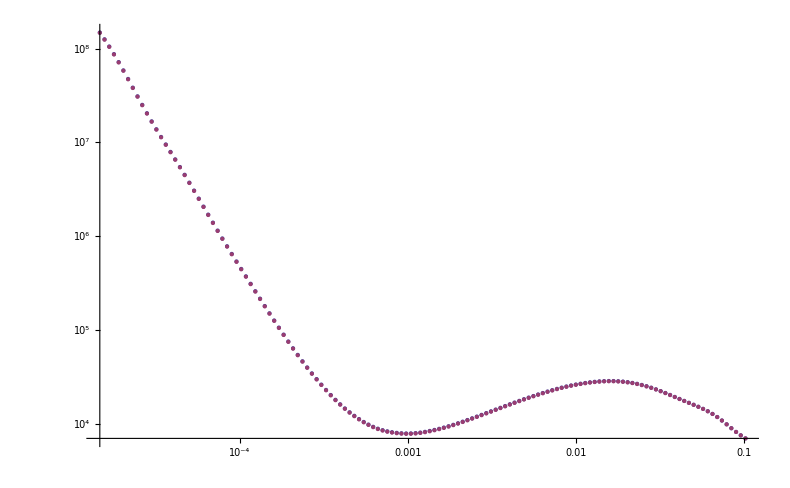

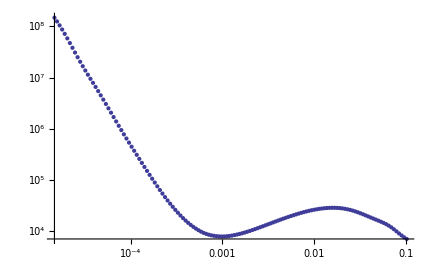
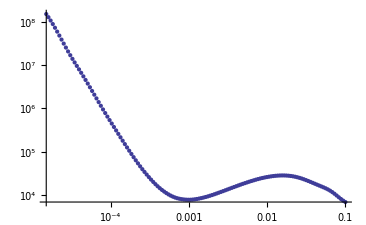

```mathematica
ListLogLogPlot[{power,PowerL}]
Table[{ListLogLogPlot[{PowerL}],ListLogLogPlot[power]}]
```

{{0.0000147064,0.00460887},{0.0000156873,0.00460887},{0.0000167336,0.00460887},{0.0000178496,0.00460887},{0.0000190402,0.00460887},{0.0000203101,0.00460887},{0.0000216647,0.00460887},{0.0000231097,0.00460887},{0.000024651,0.00460887},{0.0000262952,0.00460887},{0.000028049,0.00460887},{0.0000299197,0.00460887},{0.0000319153,0.00460887},{0.0000340439,0.00460887},{0.0000363146,0.00460887},{0.0000387366,0.00460887},{0.0000413202,0.00460887},{0.0000440762,0.00460887},{0.0000470159,0.00460887},{0.0000501517,0.00460887},{0.0000534967,0.00460887},{0.0000570647,0.00460887},{0.0000608708,0.00460887},{0.0000649306,0.00460887},{0.0000692613,0.00460887},{0.0000738808,0.00460887},{0.0000788084,0.00460887},{0.0000840647,0.00460887},{0.0000896716,0.00460887},{0.0000956524,0.00461601},{0.000102032,0.00462217},{0.000108837,0.00462728},{0.000116096,0.00463123},{0.00012384,0.00463397},{0.000132099,0.00463546},{0.00014091,0.0046357},{0.000150308,0.00463476},{0.000160333,0.00463272},{0.000171027,0.00462972},{0.000182434,0.00462593},{0.000194602,0.00462152},{0.000207581,0.00461671},{0.000221426,0.00461169},{0.000236194,0.00460664},{0.000251948,0.00460174},{0.000268752,0.00459709},{0.000286677,0.0045928},{0.000305797,0.00458889},{0.000326193,0.00458539},{0.000347949,0.00458225},{0.000371156,0.00457941},{0.000395911,0.00457679},{0.000422317,0.00457428},{0.000450484,0.00457179},{0.00048053,0.00456921},{0.00051258,0.00456645},{0.000546768,0.00456343},{0.000583235,0.00456006},{0.000622135,0.00455628},{0.00066363,0.00455204},{0.000707892,0.00454731},{0.000755106,0.00454203},{0.000805469,0.0045362},{0.000859191,0.00452978},{0.000916496,0.00452277},{0.000977624,0.00451515},{0.00104283,0.0045069},{0.00111238,0.00449802},{0.00118657,0.0044885},{0.00126571,0.00447832},{0.00135013,0.00446746},{0.00144018,0.00445593},{0.00153624,0.00444371},{0.0016387,0.00443077},{0.001748,0.00441711},{0.00186458,0.00440271},{0.00198895,0.00438754},{0.0021216,0.0043716},{0.00226311,0.00435485},{0.00241405,0.00433726},{0.00257506,0.00431883},{0.00274681,0.00429951},{0.00293001,0.00427928},{0.00312543,0.00425811},{0.00333389,0.00423596},{0.00355625,0.00421281},{0.00379344,0.0041886},{0.00404645,0.00416332},{0.00431633,0.00413691},{0.00460422,0.00410933},{0.0049113,0.00408055},{0.00523887,0.0040505},{0.00558829,0.00401916},{0.00596101,0.00398646},{0.00635859,0.00395235},{0.00678269,0.00391678},{0.00723507,0.00387969},{0.00771763,0.00384103},{0.00823237,0.00380073},{0.00878144,0.00375872},{0.00936714,0.00371495},{0.0099919,0.00366934},{0.0106583,0.00362182},{0.0113692,0.00357232},{0.0121275,0.00352076},{0.0129364,0.00346706},{0.0137992,0.00341114},{0.0147195,0.00335291},{0.0157013,0.00329229},{0.0167485,0.00322919},{0.0178656,0.00316352},{0.0190571,0.00309516},{0.0203282,0.00302404},{0.021684,0.00295004},{0.0231303,0.00287306},{0.024673,0.00279299},{0.0263186,0.00270973},{0.028074,0.00262315},{0.0299464,0.00253314},{0.0319438,0.00243957},{0.0340743,0.00234234},{0.0363469,0.00224131},{0.0387712,0.00213635},{0.0413571,0.00202734},{0.0441155,0.00191415},{0.0470578,0.00179663},{0.0501964,0.00167466},{0.0535444,0.0015481},{0.0571156,0.00141681},{0.0609251,0.00128066},{0.0649886,0.0011395},{0.0693231,0.000993205},{0.0739467,0.000841631},{0.0788787,0.000684645},{0.0841397,0.000522116},{0.0897515,0.000353914},{0.0957377,0.000179915},{0.102123,0.}}

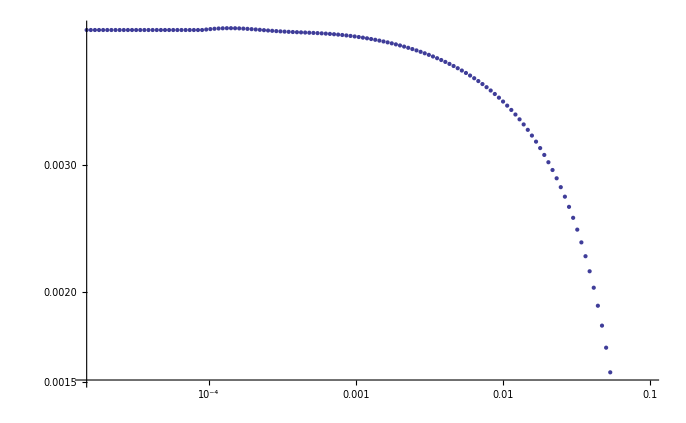

```mathematica
deltaqFac=Table[{qFac[[i,1]],qFac[[i,2]]-1},{i,1,lent}]
ListLogLogPlot[deltaqFac]
```

## Backup here

```mathematica
Clear[H]
fRFriedmann=3(1+fR)==3 H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3a H[a]^2 fRR R1//FullSimplify
```

1/(a (4083.21+44159.2 a^3))(-1.54295×10^7+a (-2.31729×10^21+a^2 (-8.34337×10^8+a (-1.50363×10^23+a^2 (-1.80464×10^10+a (-4.06528×10^24+a^2 (-1.95169×10^11+a (-5.86217×10^25+a^2 (-1.05536×10^12-4.75544×10^26 a-2.2827×10^12 a^3-2.05771×10^27 a^4-3.71063×10^27 a^7))))))))+a^12 (-1.4712×10^16-3.68255×10^19 a-1.59108×10^17 a^3-3.98261×10^20 a^4) H[a]^2)==0

```mathematica
Solve[ H[a]^2==(3 c^2)/(3a fRR R1) H0^2/c^2(Ωm0 a^-3+Ωr0 a^-4)+((1-fR)R-f)/2-3(1+fR),H[a]]
```

Solve::ratnz: Solve was unable to solve the system with inexact coefficients. The answer was obtained by solving a corresponding exact system and numericizing the result.

{{H[a]→-3.90141×10^-47 √(1.4504×10^97-(4.39723×10^114)/((44159.2+4083.21/a^3)^5)+(2.76564×10^98)/((44159.2+4083.21/a^3)^4)+(1.18683×10^108)/((44159.2+4083.21/a^3)^3)-(1.49292×10^92)/((44159.2+4083.21/a^3)^2)-(2.74514×10^95)/(0.0003236+0.81 a)-(2.00672×10^91)/((0.0003236+0.81 a) a^12)-(6.69735×10^94)/((0.0003236+0.81 a) a^11)-(8.68094×10^92)/((0.0003236+0.81 a) a^9)-(2.89722×10^96)/((0.0003236+0.81 a) a^8)-(1.40824×10^94)/((0.0003236+0.81 a) a^6)-(4.69994×10^97)/((0.0003236+0.81 a) a^5)+(1.34131×10^96)/a^3-(4.06538×10^113)/((44159.2+4083.21/a^3)^5 a^3)+(1.09726×10^107)/((44159.2+4083.21/a^3)^3 a^3)-(1.01532×10^95)/((0.0003236+0.81 a) a^3)-(3.3886×10^98)/((0.0003236+0.81 a) a^2)-(9.16176×10^98 a)/(0.0003236+0.81 a))},{H[a]→3.90141×10^-47 √(1.4504×10^97-(4.39723×10^114)/((44159.2+4083.21/a^3)^5)+(2.76564×10^98)/((44159.2+4083.21/a^3)^4)+(1.18683×10^108)/((44159.2+4083.21/a^3)^3)-(1.49292×10^92)/((44159.2+4083.21/a^3)^2)-(2.74514×10^95)/(0.0003236+0.81 a)-(2.00672×10^91)/((0.0003236+0.81 a) a^12)-(6.69735×10^94)/((0.0003236+0.81 a) a^11)-(8.68094×10^92)/((0.0003236+0.81 a) a^9)-(2.89722×10^96)/((0.0003236+0.81 a) a^8)-(1.40824×10^94)/((0.0003236+0.81 a) a^6)-(4.69994×10^97)/((0.0003236+0.81 a) a^5)+(1.34131×10^96)/a^3-(4.06538×10^113)/((44159.2+4083.21/a^3)^5 a^3)+(1.09726×10^107)/((44159.2+4083.21/a^3)^3 a^3)-(1.01532×10^95)/((0.0003236+0.81 a) a^3)-(3.3886×10^98)/((0.0003236+0.81 a) a^2)-(9.16176×10^98 a)/(0.0003236+0.81 a))}}

```mathematica
Clear[Sol]
Sol[a_]=NDSolve[{fRFriedmann,H[10^-3]==HL[10^-3,H0,Ωm0,Ωr0,Ωx0],H'[10^-3]==HL1[10^-3,H0,Ωm0,Ωr0,Ωx0]},H[a],{a,10^-4,1}]
```

NDSolve::ivcon: The given initial conditions were not consistent with the differential-algebraic equations. NDSolve will attempt to correct the values.

NDSolve::icfail: Unable to find initial conditions that satisfy the residual function within specified tolerances. Try giving initial conditions for both values and derivatives of the functions.

{}

Testing Functions

```mathematica
t1=Table[i*10^-4,{i,1,10,0.1}];
t2=Table[i*10^-3,{i,1,10,0.1}];
t3=Table[i*10^-2,{i,1,10,0.1}];
t4=Table[i*10^-1,{i,1,10,0.1}];
t5=Table[i,{i,1,1,0.1}];
aTable=Join[t1,t2,t3,t4,t5];
Length[aTable]
ListPlot[aTable];
```

365

Part::partw: Part 1 of {} does not exist.

General::stop: Further output of Part :: partw will be suppressed during this calculation.

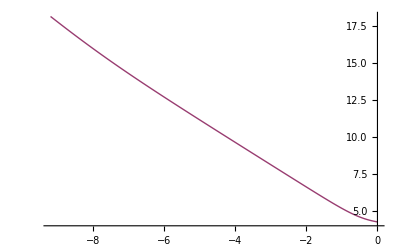

```mathematica
HubbleTable=Table[{Sol[aTable[[i]]][[1]][[1]],HL[aTable[[i]],H0,Ωm0,Ωr0,Ωx0],aTable[[i]]},{i,1,365}];
ListPlot[{Table[{Log[HubbleTable[[i]][[3]]],Log[H[HubbleTable[[i]][[3]]]/.HubbleTable[[i]][[1]]]},{i,1,365}],Table[{Log[HubbleTable[[i]][[3]]],Log[HubbleTable[[i]][[2]]]},{i,1,365}]},Joined->True]
```

ΛCDM as an example

-1-(0.333333 (-0.0003236/a^5-0.81/a^4) a)/(0.73+0.0000809/a^4+0.27/a^3)

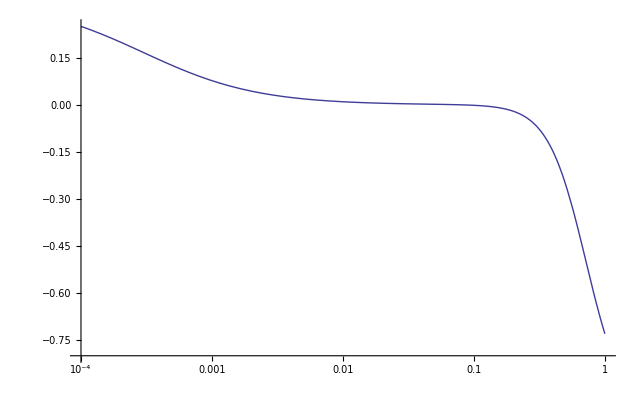

-194729.+3.56799×10^8 a^(1/9)-1.18914×10^9 a^(1/8)+1.55755×10^9 a^(1/7)-1.01651×10^9 a^(1/6)+3.45971×10^8 a^(1/5)-5.86945×10^7 a^(1/4)+4.31573×10^6 a^(1/3)-101465. √a+382.796 a

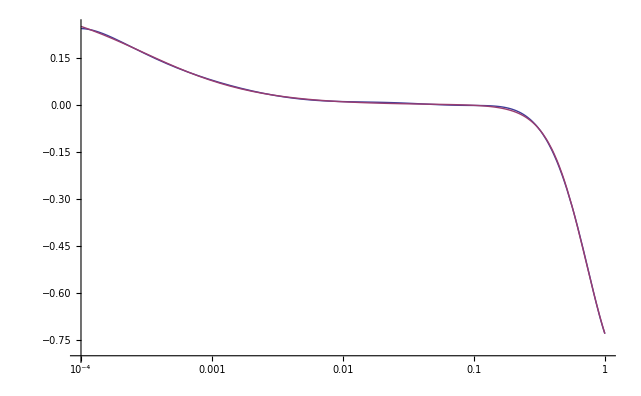

```mathematica
wleff[a_]=-1-2(a HL[a,H0,Ωm0,Ωr0,Ωx0] HL1[a,H0,Ωm0,Ωr0,Ωx0])/(3 HL[a,H0,Ωm0,Ωr0,Ωx0]^2)
LogLinearPlot[wleff[a],{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
wlefff=Table[{aTable[[i]],wleff[aTable[[i]]]},{i,1,365}];
wlefffit[a_]=Fit[wlefff,{1,a,a^(1/2),a^(1/3),a^(1/4),a^(1/5),a^(1/6),a^(1/7),a^(1/8),a^(1/9)},a]
LogLinearPlot[{wlefffit[a],wleff[a]},{a,10^-4,1},AxesOrigin-> {10^-4,-0.8}]
```

```mathematica
H1[a_]=D[H[a]/.Sol[a][[1]][[1]],a];
H[a_]=H[a]/.Sol[a][[1]][[1]];
LogLogPlot[{H[a],Abs[H1[a]]},{a,10^-4,1}];
LogLogPlot[Abs[H1[a]],{a,10^-4,1}];
weff[xx_]=-1-2(H[1/xx] H1[1/xx])/(xx 3 H[1/xx]^2);
LogLinearPlot[weff[a],{a,10^-4,1}]
wefff=Table[{aTable[[i]],weff[aTable[[i]]]},{i,1,365}];
wefffit[xx_]=Fit[wefff,{1,xx,xx^2,xx^3,xx^4,xx^5},xx]
(*wefffit[a_]=Fit[wefff,{1,a^-1,a^(-1/2),a^(-1/3),a^(-1/4),a^(-1/5)},a]*)
LogLinearPlot[{wefffit[a],weff[a]},{a,10^-4,1}]
```

Part::partw: Part 1 of {} does not exist.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.21034 is not a valid variable.

General::ivar: -9.02955 is not a valid variable.

General::ivar: -8.83356 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: -9.21015 is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: -9.02219 is not a valid variable.

General::ivar: -8.83422 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::ivar: 1/xx is not a valid variable.

$IterationLimit::itlim: Iteration limit of 4096 exceeded.

General::stop: Further output of $IterationLimit :: itlim will be suppressed during this calculation.

General::ivar: 1/a is not a valid variable.

General::ivar: -0.108576 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::ivar: 8333.33 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

0.28152 xx^4 (9.71409 (-1-(6666.67 ∂_10000. Hold[H[1/0.0001]])/Hold[H[1/0.0001]])+9.70173 (-1-(6060.61 ∂_9090.91 Hold[H[1/0.00011]])/Hold[H[1/0.00011]])+9.68938 (-1-(«18» «1»«1»)/Hold[H[«1»]])+«498»)+0.215639 xx^2 (4.78441 (-1-(«18» ∂_(«1») «1»)/Hold[H[1/(«7»)]])+«488»)+«3»+0.251651 xx^3 («585»+140.096 (-1-(«19» «1»«1»)/Hold[H[1/(«3»)]]))

General::ivar: 1/a is not a valid variable.

General::ivar: 10000. is not a valid variable.

General::ivar: 9090.91 is not a valid variable.

General::stop: Further output of General :: ivar will be suppressed during this calculation.

-Graphics-

```mathematica
TTT[a_]=(-d2 (1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^2))/(2d2 1/m^2 1/((3 H0^2/m^2(Ωm0 a^-3+Ωr0 a^-4)+2d1)^3))-3 H0^2(Ωm0 a^-3+Ωr0 a^-4)-2d1 m^2)a^2
TTT[10^-3]
TTT[10^-2]
TTT[10^-1]
TTT[1]
```

a^2 (-15123. (0.0000809/a^4+0.27/a^3)-32.4444 m^2-0.5 (32.4444+(15123. (0.0000809/a^4+0.27/a^3))/m^2) m^2)

(-5.30666×10^12-32.4444 m^2-0.5 (32.4444+(5.30666×10^12)/m^2) m^2)/1000000

(-4.20556×10^9-32.4444 m^2-0.5 (32.4444+(4.20556×10^9)/m^2) m^2)/10000

1/100 (-4.09544×10^6-32.4444 m^2-0.5 (32.4444+(4.09544×10^6)/m^2) m^2)

-4084.43-32.4444 m^2-0.5 (32.4444+4084.43/m^2) m^2